LUCAS LARSSON
DENNIS HADZIALIC            
INLÄMNINGSUPPGIFT 3

## Uppgiften

Lös nedanstående problem. Problemets lösning och resultat skall innehålla visualisering där det är relevant.
Tänk på följande:
1. Använd lämpliga stilar från meny Format->Style, i notebooken.
2. När ni skriver formler i text-celler, använd matematisk stil (se datorövning 1).
3. Glöm inte att ange namn och enhet för axlarna i grafer.

#### 1. Trafikflöde

Den här uppgiften går ut på och visa hur man kan använda linjära ekvationssystem för att studera trafikflödet genom ett trafiksystem. Trafiksystemet består av gator och korsningar där gatorna möts. Varje gata har ett visst flöde, som mäts i fordon per tidenhet. Vi skall beräkna trafikflödet för alla gatorna i trafiksystemet, givet flödet in till trafiksystemet.  Vi gör ett  viktigt antagande: Trafikflödet bevaras i varje korsning. Det betyder att ett fordon som når en korsning måste fortsätta genom trafiksystemet. Ett positivt värde på flödet flyter i pilens riktning och ett negativt flöde flyter i motsatt riktning.

Uppgift

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
b) Vilka andra förenklingar har vi antagit?

Studera vägssystemet i figur 1. Siffrorna anger trafikflödena i fordon per timme. Alla vägar är enkelriktade och trafiken följer pilarnas riktning.
b) Ställ upp ekvationssystemet.
c) Bestäm trafikflödet för vägsystemet.
d) Om trafikflödet för en av x, y, z eller w begränsas till 100 fordon per timme på grund av vägarbete. Vad blir trafikflödet för de andra vägarna?

figur 1. Diagram av vägsystem i Kumasi, Ghana (efter Adu et al. [2014])

SVAR

A- Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?

Antagandet är gilltig i de flesta fall, de enstaka fall som kan hindra att olyckor exempelvis med detta kommer enbart påverka försäningar men inga total stop, eftersom foirdon kommer tas bort till slut så att andra foroden kan paserra.

B-Vilka andra förenklingar har vi antagit?

C-Ställ upp ekvationsststemet

```mathematica
Quit[]
w+z==516;
x+y==225;
z+y==340;
```

D-Bestäm  trafikflödet vägsystemet.

```mathematica
p=Reduce[{w+z==516, z+y==340,x+y==255},{x,y,z,w}]
```

y==255-x&&z==85+x&&w==431-x

```mathematica
Reduce[p]
```

y==340-z&&x==-85+z&&w==516-z

E - Om trafikflödet för en avx, y, zellerwbegränsas till 100 fordon per timme på grund av vägarbete.Vad blir trafikflödet för de andra vägarna?

```mathematica
z=100
Reduce[p]
```

100

y==240&&x==15&&w==416

```mathematica
Clear[z]
```

```mathematica
w=100
```

100

```mathematica
Reduce[p]
```

z==416&&y==-76&&x==331

```mathematica
Clear[w,z]
```

```mathematica
y=100
Re[p]
```

100

Re[100==255-x&&z==85+x&&w==431-x]

```mathematica
Clear[w,z,y]
```

```mathematica
Reduce[p]
```

y==340-z&&x==-85+z&&w==516-z

#### 2. Kaniner

Leonardo av Pisa, även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning. Han modellerade förökning av kaniner. Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön. Modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:

p_(n+2)=p_(n+1)+p_n

där vi antar att vi har bara ett kaninpar vid månad n=1, dvs intialvärdena är p_1=1 och p_2=1. Vilket betyder att p_3=2,  p_4=3 och p_5=5.

a) Beräkna talföljden och rita en graf över den.
b) Undersök talföljden och diskutera tillväxtakten.
c) Vilka begränsningar har modellen?
d) Hur kan man förbättra modellen?
SVAR

A-Beräkna talföljden och rita en graf över den.
-Kaninernas antal förökar med 1 par per månad.
-månad 1,  n=1
-a_n   är antal per månad , Detta ger: 
a_(n+2)=a_(n+1)+a_n vilklet skrives om som
 a_n=a_(n+2)-a_(n+1) 
 a_n=a_(n-1)+a_(n-2).

```mathematica
a[1]=1;
a[2]=1;
a[n_]:=a[n-1]+a[n-2]
```

```mathematica
KaninAntal=Table[a[n],{n,1,32}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309}

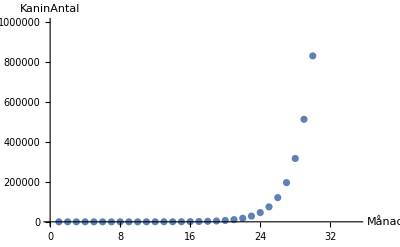

```mathematica
ListPlot[KaninAntal,AxesLabel->{"Månad","KaninAntal"},PlotRange->{{0,35},{-1000,1000000}}]
```

B-Undersök talföljden och diskutera tillväxtakten.
Ovanstånde  funktion beskriver ökningen av Kanin Antalet med avseende på tid uttryckt genom enheten månad.
Funktionen kan uttnjitas så att den visar exakta värden vid exakta tidpunkter.  
Funktionen uttsyande tyder på att den liknar en exponential funktion i dess tillväxt.

```mathematica
ListOverKaninAntal=N [Table[a[n],{n,1,33}]]
```

{1.,1.,2.,3.,5.,8.,13.,21.,34.,55.,89.,144.,233.,377.,610.,987.,1597.,2584.,4181.,6765.,10946.,17711.,28657.,46368.,75025.,121393.,196418.,317811.,514229.,832040.,1.34627×10^6,2.17831×10^6,3.52458×10^6}

C- Villka begränsningar har modellen? 
Modellen tar inte hänsyn till :1 kaniner dör,2 lika/olika kön fötts.

D- Hur kan man förbättra modellen?
En modell kan utförs som beskriver de olika faktorar som orsaker minskningingen av Kanin Antalet. faktorer såsom(dödsfall,lika/olika kön mm )